## Initialisation

```mathematica
rpoints=Import[FileNameJoin[{NotebookDirectory[],"random_points.csv"}]];
```

```mathematica
kellycols=RGBColor/@({{230,25,75},{60,180,75},(*{255,225,25},*){0,130,200},{245,130,48},{145,30,180},{70,240,240},{240,50,230},{210,245,60},{250,190,212},{0,128,128},{220,190,255},{170,110,40},{255,250,200},{128,0,0},{170,255,195},{128,128,0},{255,215,180},{0,0,128},{128,128,128},{255,255,255},{0,0,0}}/255)
```

{RGBColor[{Rational[46, 51], Rational[5, 51], Rational[5, 17]}],RGBColor[{Rational[4, 17], Rational[12, 17], Rational[5, 17]}],RGBColor[{0, Rational[26, 51], Rational[40, 51]}],RGBColor[{Rational[49, 51], Rational[26, 51], Rational[16, 85]}],RGBColor[{Rational[29, 51], Rational[2, 17], Rational[12, 17]}],RGBColor[{Rational[14, 51], Rational[16, 17], Rational[16, 17]}],RGBColor[{Rational[16, 17], Rational[10, 51], Rational[46, 51]}],RGBColor[{Rational[14, 17], Rational[49, 51], Rational[4, 17]}],RGBColor[{Rational[50, 51], Rational[38, 51], Rational[212, 255]}],RGBColor[{0, Rational[128, 255], Rational[128, 255]}],RGBColor[{Rational[44, 51], Rational[38, 51], 1}],RGBColor[{Rational[2, 3], Rational[22, 51], Rational[8, 51]}],RGBColor[{1, Rational[50, 51], Rational[40, 51]}],RGBColor[{Rational[128, 255], 0, 0}],RGBColor[{Rational[2, 3], 1, Rational[13, 17]}],RGBColor[{Rational[128, 255], Rational[128, 255], 0}],RGBColor[{1, Rational[43, 51], Rational[12, 17]}],RGBColor[{0, 0, Rational[128, 255]}],RGBColor[{Rational[128, 255], Rational[128, 255], Rational[128, 255]}],RGBColor[{1, 1, 1}],RGBColor[{0, 0, 0}]}

```mathematica
line1=Range[-15,15,30/500];
line2=Range[-2,3,5/500];
fpoints=Tuples[{line1,line2}];
```

## Square

```mathematica
lines=ContourPlot[{(2-1/(1+ⅇ^(β μ))-ⅇ^β/(ⅇ^β+ⅇ^(β μ)))/2==0.250368,(1-1/(1+ⅇ^(β μ)))^4(1-1/(1+ⅇ^(β (μ-1))))^4==0.407,1/128 (18+16 Cosh[β]+Cosh[2 β]) Sech[(β μ)/2]^4 Sech[1/2 (β-β μ)]^4==0.59274,(1/(1+ⅇ^(β μ)))^4(1/(1+ⅇ^(β (μ-1))))^4==0.59274},{μ,-2,3},{β,-15,15},AspectRatio->1,ContourStyle->Directive[Thickness[0.007],kellycols[[6]]](*ContourStyle->{Red,RGBColor[0.09,0.87,1],RGBColor[0.7,1,0],RGBColor[1,0.35,0]*),LabelStyle->Directive[Bold,16],ImageSize->400,FrameLabel->{"μ","β"},PlotPoints->100];
```

```mathematica
squareData=Import[FileNameJoin[{NotebookDirectory[],"out_100_128_random_points.csv"}]];
```

```mathematica
transplts=GraphicsGrid[{
{ListPointPlot3D[{#1[[1]],#1[[2]],#2}&@@@Transpose[{rpoints,#[[1]]&/@squareData}],ColorFunction->(ColorData["Rainbow"][#3]&),LabelStyle->Directive[Bold, 14],AxesLabel->{"β","μ","P"},PlotLabel->"I",ImageSize->600],
ListPointPlot3D[{#1[[1]],#1[[2]],#2}&@@@Transpose[{rpoints,#[[2]]&/@squareData}],ColorFunction->(ColorData["Rainbow"][#3]&),LabelStyle->Directive[Bold, 14],AxesLabel->{"β","μ","P"},PlotLabel->"II",ImageSize->600]},
{ListPointPlot3D[{#1[[1]],#1[[2]],#2}&@@@Transpose[{rpoints,#[[3]]&/@squareData}],ColorFunction->(ColorData["Rainbow"][#3]&),LabelStyle->Directive[Bold, 14],AxesLabel->{"β","μ","P"},PlotLabel->"III",ImageSize->600,PlotRange->{0,1}],
ListPointPlot3D[{#1[[1]],#1[[2]],#2}&@@@Transpose[{rpoints,#[[4]]&/@squareData}],ColorFunction->(ColorData["Rainbow"][#3]&),LabelStyle->Directive[Bold, 14],AxesLabel->{"β","μ","P"},PlotLabel->"IV",ImageSize->600]}
},ImageSize->1000]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","sqTrans.png"}],transplts]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\sqTrans.png

```mathematica
classedSquareData=StringJoin[ToString@Boole[#>0.45]&/@#]&/@squareData;
```

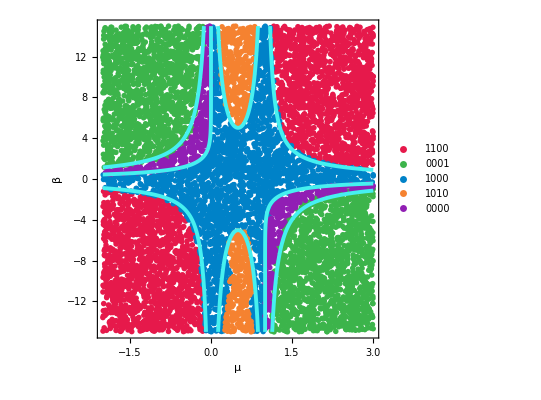

```mathematica
plt1=Show[ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedSquareData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", 4},Frame->True,PlotStyle->Take[kellycols,5],PlotLegends->{"1100","0001","1000","1010","0000"},Axes->False,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},AspectRatio->1,PlotRange->{{-2,3},{-15,15}}],lines]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","sqPhase1.png"}],plt1]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\sqPhase1.png

```mathematica
squareClassifier=ClassifierFunction[…]
```

ClassifierFunction[…]

```mathematica
classedSquareArray=Partition[squareClassifier[fpoints],Length[line1]];
```

```mathematica
arrplt1=Show[ListPlot[{{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}}},PlotRange->{{-2,3},{-15,15}},Frame->True,PlotStyle->Take[kellycols,5],PlotLegends->{"1100","0001","1000","1010","0000"},Axes->False,LabelStyle->Directive[Bold, 12],FrameLabel->{"μ","β"},AspectRatio->1],ArrayPlot[classedSquareArray/.{"1100"->kellycols[[1]],"0001"->kellycols[[2]],"1000"->kellycols[[3]],"1010"->kellycols[[4]],"0000"->kellycols[[5]]},DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1,Frame->True]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","sqArr.png"}],arrplt1]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\sqArr.png

## Cube

```mathematica
cubeData=Import[FileNameJoin[{NotebookDirectory[],"out_20_128_random_points.csv"}]];
```

```mathematica
classedCubeData=StringJoin[ToString@Boole[#>0.45]&/@Drop[Drop[Drop[Drop[Drop[#,{2,6}],{3}],{4,12}],{5}],{6,10}]]&/@cubeData;
```

```mathematica
Last/@Last/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&]
```

{1000010,0000001,1000000,1010000,0000000,1100000,1000100,1001000}

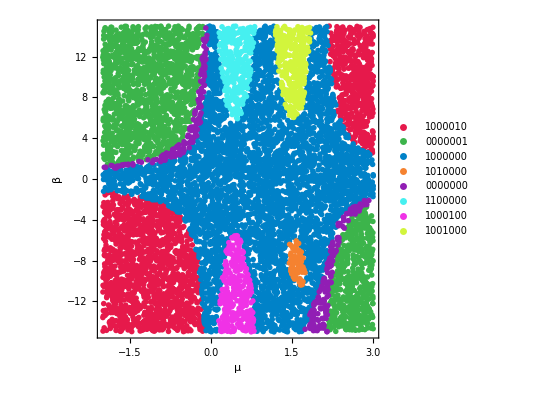

```mathematica
plt2=ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", 4},Frame->True,PlotStyle->Take[kellycols,8],PlotLegends->(Last/@Last/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&]),Axes->False,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},AspectRatio->1,PlotRange->{{-2,3},{-15,15}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","cbPhase1.png"}],plt2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\cbPhase1.png

```mathematica
cubeClassifier=Classify[rpoints->classedCubeData,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

```mathematica
classedCubeArray=Partition[cubeClassifier[fpoints],Length[line1]];
```

```mathematica
cols=#1->#2&@@@Transpose[{#,Take[kellycols,Length[#]]}&@(Last/@Last/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&])];
```

```mathematica
arrplt2=Show[ListPlot[{{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}}},PlotRange->{{-2,3},{-15,15}},Frame->True,PlotStyle->Take[kellycols,8],PlotLegends->(Last/@Last/@GatherBy[Transpose[{rpoints,classedCubeData}],#[[2]]&]),Axes->False,LabelStyle->Directive[Bold, 12],FrameLabel->{"μ","β"},AspectRatio->1],ArrayPlot[classedCubeArray/.cols,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1,Frame->True]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","cbArr.png"}],arrplt2]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\cbArr.png

## Hex

```mathematica
hexData=Import[FileNameJoin[{NotebookDirectory[],"out_70_128_random_points.csv"}]];
```

```mathematica
classedHexData=StringJoin[ToString@Boole[#>0.45]&/@Drop[Drop[Drop[Drop[#,{2,3}],{3,5}],{3,4}],{4,5}]]&/@hexData;
```

```mathematica
DeleteDuplicates[classedHexData]
```

{10010,00001,10000,11000,00000,10100}

```mathematica
hexClassifier=Classify[rpoints->classedHexData,Method->"NeuralNetwork",TargetDevice->"GPU"]
```

ClassifierFunction[…]

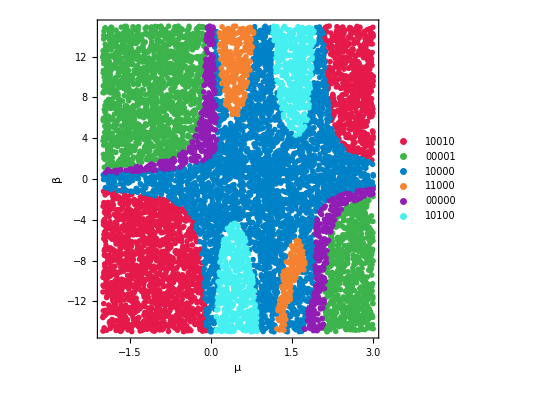

```mathematica
plt3=ListPlot[{#1[[2]],#1[[1]]}&@@@#&/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&],AspectRatio->1,PlotMarkers->{"OpenMarkers", 4},Frame->True,PlotStyle->Take[kellycols,6],PlotLegends->(Last/@Last/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&]),Axes->False,LabelStyle->Directive[Bold, 14],FrameLabel->{"μ","β"},AspectRatio->1,PlotRange->{{-2,3},{-15,15}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","hxPhase1.png"}],plt3]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\hxPhase1.png

```mathematica
classedHexArray=Partition[hexClassifier[fpoints],Length[line1]];
```

```mathematica
cols2=#1->#2&@@@Transpose[{#,Take[kellycols,Length[#]]}&@(Last/@Last/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&])];
```

```mathematica
arrplt3=Show[ListPlot[{{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}},{{-1000,-1000}}},PlotRange->{{-2,3},{-15,15}},Frame->True,PlotStyle->Take[kellycols,6],PlotLegends->(Last/@Last/@GatherBy[Transpose[{rpoints,classedHexData}],#[[2]]&]),Axes->False,LabelStyle->Directive[Bold, 12],FrameLabel->{"μ","β"},AspectRatio->1],ArrayPlot[classedHexArray/.cols2,DataReversed->True,DataRange->{{-2,3},{-15,15}},AspectRatio->1,Frame->True]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","hxArr.png"}],arrplt3]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\hxArr.png

```mathematica
hxgrph=Rasterize[GraphPlot[Graph@Join[Import["C:\\Users\\jfdup\\PCSync\\Physics 344\\Graph Phases\\Ass4\\graphs\\hex\\70x70\\1.el"]],PlotTheme->"LargeGraph"],ImageSize->600]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","hxGr.png"}],hxgrph]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\hxGr.png

## Percolation exponents

```mathematica
nlm1=FittedModel[1.4215412027801813 (-0.00014719969287001428+μ)^0.10232616817393815]
nlm2=FittedModel[0.7021482652445626 (1-μ)^0.09834752519847867]
nlm4=FittedModel[1.2083906683856092 (0.19984427975213995-β)^0.0959852747165792]
nlm5=FittedModel[1.2219539580474592 (0.24452964855598716+β)^0.10700578994036705]
```

FittedModel[1.42154 (-0.0001472+μ)^0.102326]

FittedModel[0.702148 (1-μ)^0.0983475]

FittedModel[1.20839 (0.199844-β)^0.0959853]

FittedModel[1.22195 (0.24453+β)^0.107006]

```mathematica
percs=GraphicsGrid[{
{Show[ListPlot[Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],"sqMuplt_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqMuplt_points.csv"}]]}],Frame->True,Axes->False,PlotMarkers->{Automatic, Small},PlotStyle->kellycols[[18]],LabelStyle->Directive[Bold, 18],FrameLabel->{"μ","P"},PlotLegends->{"Data"},PlotLabel->"β=20",ImageSize->400],Plot[nlm1[μ],{μ,0,0.1},PlotStyle->{Dashed,Red},PlotRange->All,PlotPoints->1000,LabelStyle->Directive[Bold, 18],PlotLegends->{"Powerlaw fit"}]],
Show[ListPlot[Transpose[{Last/@Import[FileNameJoin[{NotebookDirectory[],"sqMuplt2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqMuplt2_points.csv"}]]}],Frame->True,Axes->False,PlotMarkers->{Automatic, Small},PlotStyle->kellycols[[18]],LabelStyle->Directive[Bold, 18],FrameLabel->{"μ","P"},PlotLabel->"β=-20",ImageSize->450],Plot[nlm2[μ],{μ,0.9,1.1},PlotStyle->{Dashed,Red},PlotRange->All,PlotPoints->1000,LabelStyle->Directive[Bold, 18]]]},
{Show[ListPlot[Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBetaplt_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqBetaplt_points.csv"}]]}],Frame->True,Axes->False,PlotMarkers->{Automatic, Small},PlotStyle->kellycols[[2]],LabelStyle->Directive[Bold, 18],FrameLabel->{"β","P"},PlotLegends->{"Data"},PlotLabel->"μ=-5",ImageSize->400],Plot[nlm4[β],{β,0,1},PlotStyle->{Dashed,Red},PlotRange->All,PlotPoints->1000,LabelStyle->Directive[Bold, 18],PlotLegends->{"Powerlaw fit"}]],
Show[ListPlot[Transpose[{First/@Import[FileNameJoin[{NotebookDirectory[],"sqBetaplt2_points.csv"}]],First/@Import[FileNameJoin[{NotebookDirectory[],"out_100_64_sqBetaplt2_points.csv"}]]}],Frame->True,Axes->False,PlotMarkers->{Automatic, Small},PlotStyle->kellycols[[2]],LabelStyle->Directive[Bold, 18],FrameLabel->{"β","P"},PlotLabel->"μ=5",ImageSize->450],Plot[nlm5[β],{β,-1,0},PlotStyle->{Dashed,Red},PlotRange->All,PlotPoints->1000,LabelStyle->Directive[Bold, 18]]]}},ImageSize->1100,Spacings->{-100,0}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Report","figures","percScaling.png"}],percs]
```

C:\Users\jfdup\PCSync\Physics 344\Graph Phases\Ass4\Report\figures\percScaling.png